-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 9 III.E The H–Theorem and Irreversibility

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

```mathematica
(1) -- Hey there! Let's talk about how particles behave over time. We're curious if a bunch of particles will naturally settle into a balanced state. Now, we can find steady solutions for the whole group of particles, but because of something called time reversal symmetry, these solutions don't automatically attract other states.

But what about looking at just one particle? Well, the exact behavior of one particle has the same issue. However, there's something cool called the H-theorem. It shows that if we use an approximate description of a single particle (using what we call the Boltzmann equation), it actually does move towards a balanced state in a way that can't be reversed.

This H-theorem tells us something important about how particles behave over time. It's a key idea in understanding how things in nature tend to become more disordered or balanced.
```

(2) -- In our study of thermodynamics and statistical mechanics, we encounter an important relationship between the Boltzmann equation and a quantity called H. When a distribution function f₁(p⃗, q⃗, t) satisfies the Boltzmann equation, we find that the time derivative of H is always less than or equal to zero. This relationship, dH/dt ≤ 0, is known as the H-theorem and plays a crucial role in understanding the direction of time and the approach to equilibrium in statistical systems.

Statistical Mechanics
Ramirez (3)

```mathematica
MaTeX["\\mathrm{H}(t)=\\int d \\vec{q} f_{1}(\\vec{p}, \\vec{q}, t) \\ln f_{1}(\\vec{p}, \\vec{q}, t)\\,  d \\vec{p} ", Magnification -> 4]
```

-Graphics-

(4) -- Let's break this down into simpler terms:

The function H(t) is connected to how much information we can get from looking at a single particle in our system. Think of it as a measure of what we know about one particle's behavior.

We use something called a probability density function (PDF) to describe where a particle is likely to be. For one particle, we write this as ρ₁ = f₁/N, where N is the total number of particles.

The information content of this PDF is given by I[ρ₁] = ⟨ln ρ₁⟩. This looks a lot like our H(t) function, just with a constant difference.

In essence, H(t) tells us how uncertain we are about the state of our system over time. The more information we have, the less uncertain we are.

```mathematica
(5) -- Proof: The time derivative of $\mathrm{H}$ is
```

Statistical Mechanics
Ramirez (6)

```mathematica
MaTeX["\\frac{d \\mathrm{H}}{d t}=\\int d^3\\vec{p}_{1}d^3\\vec{q}_{1} \\frac{\\partial f_{1}}{\\partial t}\\left(\\ln f_{1}+1\\right) =\\int  d^3\\vec{p}_{1} d^3\\vec{q}_{1} \\ln f_{1} \\frac{\\partial f_{1}}{\\partial t}", Magnification -> 4]
```

-Graphics-

(7) -- since $\int d V_{1} f_{1}=N \int d \Gamma \rho=N$ is time independent. Using eq.(III.41), we obtain(7) -- Let's simplify this concept for an undergraduate:

The integral of f₁ over the volume V₁ equals N times the integral of ρ over the entire phase space Γ. This value remains constant over time and equals N, which is the total number of particles in our system. 

When we apply this to equation (III.41), we can derive some interesting results about the behavior of our system. This helps us understand how the microscopic properties of particles relate to the macroscopic properties we observe.

Statistical Mechanics
Ramirez (8)

```mathematica
MaTeX["\\begin{gathered}\\frac{d \\mathrm{H}}{d t}=\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} \\ln f_{1}\\left(\\frac{\\partial U}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\partial f_{1}}{\\partial \\vec{p}_{1}}-\\frac{\\vec{p}_{1}}{m} \\cdot \\frac{\\partial f_{1}}{\\partial \\vec{q}_{1}}\\right) \\\\-\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} d^{3} \\vec{p}_{2} d^{2} \\sigma\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}\\right) f_{1}\\left(\\vec{p}_{2}, \\vec{q}_{1}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}, \\vec{q}_{1}\\right)\\right] \\ln f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}\\right)\\end{gathered}", Magnification -> 4]
```

-Graphics-

(9) -- In our discussion of cross-sections, we'll use different notations interchangeably: d.b2σ, d.b2b⃗, or d.b2Ω|dσ/dΩ|. These all represent the differential cross-section, which describes how particles scatter in different directions.

Now, let's talk about the streaming terms in our equation. These terms end up being zero, which might seem surprising at first. We can prove this through a mathematical technique called integration by parts. We apply this technique multiple times, and each time, we find that these streaming terms cancel out.

This simplification is important because it helps us focus on the other, more significant parts of our equation when we're studying particle interactions and scattering processes.

```mathematica
MaTeX["\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} \\ln f_{1} \\frac{\partial U}{\\partial \\vec{q}_{1}} \\cdot \\frac{\partial f_{1}}{\\partial \\vec{p}_{1}}=-\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} f_{1} \\frac{\\partial U}{\\partial \\vec{q}_{1}} \\cdot \\frac{1}{f_{1}} \\frac{\\partial f_{1}}{\\partial \\vec{p}_{1}}=\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} f_{1} \\frac{\\partial}{\\partial \\vec{p}_{1}} \\cdot \\frac{\partial U}{\\partial \\vec{q}_{1}}=0,",Magnification->2.2]
```

-Graphics-

```mathematica
(10) -- Imagine we're looking at a system of particles in space. We can describe their positions and momenta using special mathematical tools. This equation tells us something important: when we consider how the particles' energy changes with their positions, and how their distribution changes with their momenta, these effects balance out perfectly. In simpler terms, it's like saying that in a well-behaved system, the way particles move and interact doesn't lead to any unexpected changes in their overall distribution. This principle is fundamental in understanding how large groups of particles behave collectively.
```

Statistical Mechanics
Ramirez (12)

```mathematica
MaTeX["\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} \\ln f_{1} \\frac{\\vec{p}_{1}}{m} \\cdot \\frac{\\partial f_{1}}{\\partial \\vec{q}_{1}}=-\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} f_{1} \\frac{\\vec{p}_{1}}{m} \\cdot \\frac{1}{f_{1}} \\frac{\\partial f_{1}}{\\partial \\vec{q}_{1}}=\\int d^{3} \\vec{p}_{1} d^{3} \\vec{q}_{1} f_{1} \\frac{\\partial}{\\partial \\vec{q}_{1}} \\cdot \\frac{\\vec{p}_{1}}{m}=0", Magnification -> 4]
```

-Graphics-

(13) -- Let's consider the collision term in our equation. It involves integrals over two variables, which we'll call p₁ and p₂. These are just placeholder names, so we can swap them around without changing the actual value of the integral. If we do this swap and then take the average of the original expression and the swapped one, we get a new, equivalent form of the collision term. This trick can sometimes make our calculations easier or reveal symmetries in the system we're studying.

Statistical Mechanics
Ramirez (14)

```mathematica
MaTeX["\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{2} \\int d \\vec{p}_{1} d \\vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right] \\ln \\left(f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right)\\,  d \\vec{q} ", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{2} \\int d \\vec{p}_{1} d \\vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right] \\ln \\left(f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right)\\,  d \\vec{q} ",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(d H)/dt==-1/2 ∫d (p⃗)_1 d (p⃗)_2 d b⃗ Abs[(v⃗)_1-(v⃗)_2][f_1[(p⃗)_1] f_1[(p⃗)_2]-f_1[(p⃗)_1'] f_1[(p⃗)_2']] Log[f_1[(p⃗)_1] f_1[(p⃗)_2]]ⅆ q⃗

```mathematica
(15) -- Let's simplify this concept a bit. Imagine we're looking at collisions between particles. At first, we describe these collisions using the initial positions and speeds of the particles (we call these p₁, p₂, and b). But sometimes it's more useful to describe the collision using the final positions and speeds of the particles after they've collided (we call these p₁', p₂', and b').

Changing from one set of descriptions to the other can be tricky mathematically. However, we have a handy principle that makes our life easier: for every collision going forward in time, there's an equal collision going backward in time. This principle, called time reversal symmetry, ensures that when we switch between these two ways of describing collisions, we don't accidentally create or lose any information.

This property is incredibly useful because it allows us to look at collisions from different perspectives without worrying about introducing errors in our calculations.
```

Statistical Mechanics
Ramirez (16)

```mathematica
MaTeX["\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{2} \\int d \\vec{p}_{1}{}^{\\prime} d \\vec{p}_{2}^{\\prime} d \\vec{b}^{\\prime}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}{}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right] \\ln \\left(f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right)\\,  d \\vec{q} ", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{2} \\int d \\vec{p}_{1}{}^{\\prime} d \\vec{p}_{2}^{\\prime} d \\vec{b}^{\\prime}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}{}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right] \\ln \\left(f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right)\\,  d \\vec{q} ",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(d H)/dt==-1/2 ∫d (p⃗)_1 ' d (p⃗)_2' d b⃗' Abs[(v⃗)_1-(v⃗)_2][f_1[(p⃗)_1] f_1[(p⃗)_2]-f_1[(p⃗)_1 '] f_1[(p⃗)_2']] Log[f_1[(p⃗)_1] f_1[(p⃗)_2]]ⅆ q⃗

(17) -- When we look at the equation, we need to think of p₁ and p₂ as functions that depend on p₁', p₂', and b'. This relationship was shown earlier in equation (III.39).

Remember, in any elastic collision, the relative velocity between the particles remains the same before and after the collision. So, we can use |v₁ - v₂| and |v₁' - v₂'| interchangeably.

To make our equation cleaner, we'll remove the prime symbols from our integration variables. It's important to note that the way (p₁, p₂, b) depends on (p₁', p₂', b') is exactly the same as how (p₁', p₂', b') depends on (p₁, p₂, b). This symmetry allows us to simplify our equation further.

Statistical Mechanics
Ramirez (18)

```mathematica
MaTeX["\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{2} \\int d \\vec{p}_{1} d \\vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)-f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right] \\ln \\left(f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right)\\,  d \\vec{q} ", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{2} \\int d \\vec{p}_{1} d \\vec{p}_{2} d \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)-f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right] \\ln \\left(f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right)\\,  d \\vec{q} ",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(d H)/dt==-1/2 ∫d (p⃗)_1 d (p⃗)_2 d b⃗ Abs[(v⃗)_1-(v⃗)_2][f_1[(p⃗)_1'] f_1[(p⃗)_2']-f_1[(p⃗)_1] f_1[(p⃗)_2]] Log[f_1[(p⃗)_1'] f_1[(p⃗)_2']]ⅆ q⃗

```mathematica
(19) -- Averaging eqs.(III.45) and (III.47) results in
```

Statistical Mechanics
Ramirez (20)

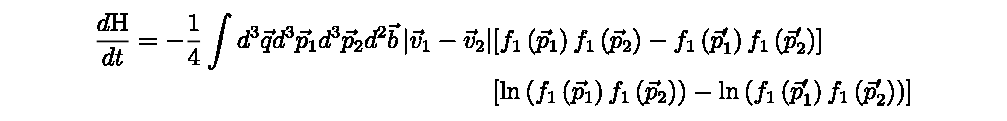

```mathematica
MaTeX["\\begin{aligned}\\frac{d \\mathrm{H}}{d t}=-\\frac{1}{4} \\int d^{3} \\vec{q} d^{3} \\vec{p}_{1} d^{3} \\vec{p}_{2} d^{2} \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right| & {\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right]} \\\\& {\\left[\\ln \\left(f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right)-\\ln \\left(f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right)\\right]}\\end{aligned}", Magnification -> 4]
```

```mathematica
(21) -- When we look at the math inside the integral, we always get a positive result. Here's why:

We're comparing two products: f₁(p₁)f₁(p₂) and f₁(p₁')f₁(p₂').

If the first product is bigger, both terms in brackets are positive.
If the second product is bigger, both terms in brackets are negative.

In either case, when we multiply these terms, we end up with a positive number.

This positive result is crucial because it proves the H-theorem, which is an important concept in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (22)

## Irreversibility

```mathematica
MaTeX["\\frac{d \\mathrm{H}}{d t} \\leq 0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\frac{d \\mathrm{H}}{d t} \\leq 0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(d H)/dt≤0

```mathematica
(23) -- Irreversibility is a key aspect of the second law of thermodynamics. It explains why we see certain processes happening in only one direction in our everyday lives. For example, a hot cup of coffee cools down over time, but we never see a cold cup of coffee spontaneously heat up.

This one-way nature of processes seems to contradict the reversible laws of physics at the microscopic level. However, computer simulations of large numbers of particles (around 10^6) following reversible laws still show irreversible behavior similar to what we observe in nature (which typically involves about 10^23 particles).

For instance, if we start with particles in one half of a box, they'll spread out to fill the entire box over time. This happens regardless of computational accuracy and can even be observed in simulations using exact integer calculations.

So, the irreversibility we see in our daily lives likely emerges from the collective behavior of many particles, even though the underlying laws governing each particle are reversible.
```

(24) -- The Boltzmann equation and time reversibility. It's pretty cool because it's the first equation we've seen that clearly doesn't work the same way if we run time backwards. This is different from most equations in physics, which usually work both ways in time.

So, how did we get this one-way-in-time equation from the regular, reversible equations of motion? Well, we made some smart guesses and approximations along the way. We ignored three-body collisions and simplified how we look at space and time. These steps didn't break time symmetry yet.

The big change came when we replaced the two-body density (which describes how two particles interact) with a simpler product of two one-body densities. This is where we lost the time reversibility. It's like we assumed the particles don't remember their past interactions, which makes the equation work only in one time direction.

This approximation is what gives the Boltzmann equation its special ability to describe how systems naturally move towards equilibrium over time, just like we see in the real world!

```mathematica
(25) -- In quantum mechanics and statistical physics. The Schrödinger equation, which describes how quantum systems evolve, works the same way whether time moves forward or backward. This seems to conflict with our everyday experience of time always moving forward.

Now, imagine we're looking at particles colliding. We usually assume the particles aren't related before they collide, but are connected after. This leads us to conclude that entropy increases over time. However, if we assumed the opposite - that particles are related before colliding but not after - we'd reach the opposite conclusion!

In reality, particles are subtly connected both before and after collisions. We often overlook these connections, especially when a system isn't in equilibrium. This oversight is part of why we see time as having a direction, even though the underlying physics doesn't distinguish between forward and backward.
```

(26) -- Let's think about molecules bouncing around like tiny billiard balls. When they collide, we can't keep track of every single detail. This is why things in nature tend to get more mixed up over time, not less.

Imagine pouring oil and water together. At first, you see clear layers. As you stir, the layers break into smaller and smaller droplets. Eventually, the mixture looks blended, even though the oil and water haven't truly mixed at the tiniest level.

In the same way, as molecules move and collide, the information about their exact positions and speeds gets spread out into tinier and tinier details. Our measurements can't capture these ultra-fine details, so we lose track of the precise information.

This is why we use probability in thermodynamics. We describe the overall behavior of many molecules instead of following each one. The more collisions occur, the more we rely on probabilities rather than exact paths.

## III.F Equilibrium Properties

(27) -- In our study of equilibrium properties, we need to consider what happens to a homogeneous gas once it reaches equilibrium. At this point, the H-function stops decreasing over time. For this to occur, we must have dH/dt = 0. 

Looking at the equation for dH/dt, we see that the integrand is always positive. Therefore, to achieve dH/dt = 0, a necessary condition is that the term inside the integrand must equal zero.

This condition gives us insight into the nature of the equilibrium distribution f₁. It tells us how the gas particles are distributed in terms of their positions and velocities once the system has settled into its equilibrium state.

Statistical Mechanics
Ramirez (28)

## Equilibrium distribution

```mathematica
MaTeX["f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}\\right) f_{1}\\left(\\vec{p}_{2}, \\vec{q}_{1}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}, \\vec{q}_{1}\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{1}\\left(\\vec{p}_{1}, \\vec{q}_{1}\\right) f_{1}\\left(\\vec{p}_{2}, \\vec{q}_{1}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}_{1}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}, \\vec{q}_{1}\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_1[(p⃗)_1,(q⃗)_1] f_1[(p⃗)_2,(q⃗)_1]-f_1[(p⃗)_1',(q⃗)_1] f_1[(p⃗)_2',(q⃗)_1]==0

```mathematica
(29) -- i.e. at each point q, we must have
```

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["\\ln f_{1}\\left(\\vec{p}_{1}, \\vec{q}\\right)+\\ln f_{1}\\left(\\vec{p}_{2}, \\vec{q}\\right)=\\ln f_{1}\\left(\\vec{p}_{1}{}^{\\prime}, \\vec{q}\\right)+\\ln f_{1}\\left(\\vec{p}_{2}{}^{\\prime}, \\vec{q}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln f_{1}\\left(\\vec{p}_{1}, \\vec{q}\\right)+\\ln f_{1}\\left(\\vec{p}_{2}, \\vec{q}\\right)=\\ln f_{1}\\left(\\vec{p}_{1}{}^{\\prime}, \\vec{q}\\right)+\\ln f_{1}\\left(\\vec{p}_{2}{}^{\\prime}, \\vec{q}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ln f_1[(p⃗)_1,q⃗]+ln f_1[(p⃗)_2,q⃗]==ln f_1[(p⃗)_1 ',q⃗]+ln f_1[(p⃗)_2 ',q⃗]

```mathematica
(31) -- In a two-body collision, we can identify several quantities that remain unchanged before and after the event. These conserved quantities are:

1. Number of particles
2. Total momentum (in all three directions)
3. Kinetic energy

For elastic collisions, these five quantities always stay the same. We can use this fact to find a general solution for the distribution function f₁. This approach helps us understand how particles behave during collisions and allows us to describe the system's overall behavior.
```

Statistical Mechanics
Ramirez (32)

```mathematica
MaTeX["\\ln f_{1}=a(\\vec{q})-\\vec{\\alpha}(\\vec{q}) \\cdot \\vec{p}-\\beta(\\vec{q})\\left(\\frac{\\vec{p}^{2}}{2 m}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln f_{1}=a(\\vec{q})-\\vec{\\alpha}(\\vec{q}) \\cdot \\vec{p}-\\beta(\\vec{q})\\left(\\frac{\\vec{p}^{2}}{2 m}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ln f_1==a[q⃗]-α⃗[q⃗]·p⃗-(β[q⃗] (p⃗)^2)/(2 m)

(33) -- In our study of thermodynamics and statistical mechanics, we often encounter systems with potential energy. Let's consider a simple way to include this potential energy U(q) in our calculations. Here, q represents the position coordinates of particles in the system. By incorporating U(q) into our equations, we can account for the effects of forces and interactions between particles. This addition allows us to more accurately describe the behavior of real-world systems, such as gases or liquids, where particles experience forces from their surroundings or each other. Remember, understanding how potential energy influences a system's behavior is crucial for predicting its thermodynamic properties and statistical behavior.

Statistical Mechanics
Ramirez (34)

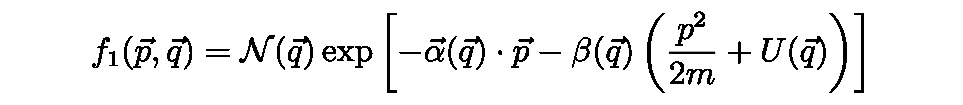

```mathematica
MaTeX["f_{1}(\\vec{p}, \\vec{q})=\\mathcal{N}(\\vec{q}) \\exp \\left[-\\vec{\\alpha}(\\vec{q}) \\cdot \\vec{p}-\\beta(\\vec{q})\\left(\\frac{p^{2}}{2 m}+U(\\vec{q})\\right)\\right]", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["f_{1}(\\vec{p}, \\vec{q})=\\mathcal{N}(\\vec{q}) \\exp \\left[-\\vec{\\alpha}(\\vec{q}) \\cdot \\vec{p}-\\beta(\\vec{q})\\left(\\frac{p^{2}}{2 m}+U(\\vec{q})\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_1[p⃗,q⃗]==N[q⃗] exp[-α⃗[q⃗]·p⃗-β[q⃗] (p^2/(2 m)+U[q⃗])]

(35) -- We shall refer to the above distribution as describing local equilibrium. While this form is preserved during collisions, it will evolve in time away from collisions, due to the streaming terms, unless $\left\{\mathcal{H}_{1}, f_{1}\right\}=0$. The latter condition is satisfied for any function $f_{1}$ that depends only on $\mathcal{H}_{1}$, or any other quantity that is conserved by it. Clearly, the above density satisfies this requirement as long as $\mathcal{N}$, and $\beta$ are independent of $\vec{q}$, and $\vec{\alpha}=0$.

(36) -- Let's consider the normalization of the one-particle distribution function f₁. To properly normalize this function, we need to ensure that the total probability of finding a particle anywhere in the system is equal to 1. This means that when we integrate f₁ over all possible positions and momenta, the result should be the total number of particles in the system, N. We can express this mathematically as:

∫∫ f₁(r,p) dr dp = N

This normalization condition is crucial for maintaining the physical meaning of our distribution function and ensuring that our calculations accurately represent the system we're studying.

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["\\int d \\vec{q} f_{1}(\\vec{p}, \\vec{q}) \\,  d \\vec{p} =N", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\int d \\vec{q} f_{1}(\\vec{p}, \\vec{q}) \\,  d \\vec{p} =N",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∫d q⃗ f_1[p⃗,q⃗]ⅆ p⃗==N

(38) -- About particles trapped in a box. Inside the box, these particles can move freely without any energy cost. But they can't escape the box - it's like there's an invisible force field at the edges that stops them from getting out.

We can describe this mathematically by saying the potential energy (U) is zero inside the box and infinitely large outside. This ensures the particles stay confined within the volume (V) of the box.

When we're calculating probabilities for these particles, we need to make sure our equations are properly scaled. We can do this by using a normalization factor, which we can find by integrating over all possible positions within the box.

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["N=\\mathcal{N} V\\left[\\int _{-\\infty}^{\\infty} \\exp \\left(-\\alpha_{i} p_{i}-\\frac{\\beta p_{i}^{2}}{2 m}\\right)\\right]^{3} \\,  d p_{i}=\\mathcal{N} V\\left(\\frac{2 \\pi m}{\\beta}\\right)^{3 / 2} \\exp \\left(\\frac{m \\alpha^{2}}{2 \\beta}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(40) -- Hence, the properly normalized Gaussian distribution for momenta is
```

Statistical Mechanics
Ramirez (41)

```mathematica
MaTeX["f_{1}(\\vec{p}, \\vec{q})=n\\left(\\frac{\\beta}{2 \\pi m}\\right)^{3 / 2} \\exp \\left[-\\frac{\\beta\\left(\\vec{p}-\\vec{p}_{0}\\right)^{2}}{2 m}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["f_{1}(\\vec{p}, \\vec{q})=n\\left(\\frac{\\beta}{2 \\pi m}\\right)^{3 / 2} \\exp \\left[-\\frac{\\beta\\left(\\vec{p}-\\vec{p}_{0}\\right)^{2}}{2 m}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

f_1[p⃗,q⃗]==n (β/(2 π m))^(3/2) exp[-(β (p⃗-(p⃗)_0)^2)/(2 m)]

```mathematica
(42) -- In a stationary box of gas, the average momentum of the particles, p₀ = <p>, is zero. Here, m is the particle mass and α/β represents the average velocity. The particle density, n, is simply the number of particles N divided by the volume V.

The momentum distribution of the gas follows a Gaussian shape. This tells us something important about the spread of momentum values. For each direction (x, y, or z), the variance of the momentum is given by <p.b2> = m/β. 

This relationship between mass, temperature (represented by β), and momentum variance is a key feature of gases in equilibrium.
```

Statistical Mechanics
Ramirez (43)

```mathematica
MaTeX["\\left\\langle p^{2}\\right\\rangle=\\left\\langle p_{x}^{2}+p_{y}^{2}+p_{z}^{2}\\right\\rangle=\\frac{3 m}{\\beta}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle p^{2}\\right\\rangle=\\left\\langle p_{x}^{2}+p_{y}^{2}+p_{z}^{2}\\right\\rangle=\\frac{3 m}{\\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨p^2⟩==⟨p_x^2+p_y^2+p_z^2⟩==(3 m)/β

## Equilibrium between two gases

```mathematica
(44) --About what happens when two different gases mix together. Imagine we have gas (a) and gas (b) floating around in the same space. They're both affected by the same overall force field, which we call U. But that's not all - the individual particles of gas A and gas B can also interact with each other. We describe this interaction with something called V_ab, which depends on how far apart the particles are.

Now, to keep track of all these particles, we use something called one-particle densities. We have f₁ᵃ for gas (a) and f₁ᵇ for gas (b). These densities tell us how the particles of each gas are spread out in space.

When the gases collide and mix, we can describe what's happening using a special mathematical tool called a generalized collision integral. This helps us understand how the particles from both gases interact and exchange energy.

That's the basic idea! We're looking at how two gases behave when they're mixed together, considering both the overall forces acting on them and how their individual particles interact.
```

```mathematica
MaTeX["C_{\\alpha, \\beta}=-\\int d^{3} \\vec{p}_{2} d^{2} \\Omega\\left|\\frac{d \\sigma_{\\alpha, \\beta}}{d \\Omega}\\right|\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}^{(\\alpha)}\\left(\\vec{p}_{1}, \\vec{q}_{1}\\right) f_{1}^{(\\beta)}\left(\\vec{p}_{2}, \\vec{q}_{1}\\right)-f_{1}^{(\\alpha)}\left(\\vec{p}_{1}{ }^{\\prime}, \\vec{q}_{1}\\right) f_{1}^{(\\beta)}\\left(\\vec{p}_{2}{ }^{\\prime}, \\vec{q}_{1}\\right)\\right]", Magnification->2]
```

-Graphics-

(45) -- Imagine we're looking at how particles of two different types, α and β, interact with each other. The equation Cα,β describes the rate at which these particles collide and exchange energy and momentum. 

To understand this, we need to consider:
1. The velocities of the particles (v1 and v2)
2. The probability of finding particles with certain momenta (p) and positions (q)
3. The likelihood of particles scattering in different directions (dσ/dΩ)

We integrate over all possible momenta and angles to get the total collision rate. The equation compares the state before and after the collision, showing how the particle distributions change.

This collision term is crucial in understanding how gases and plasmas behave, especially when we're dealing with mixtures of different particle types.

```mathematica
(46) -- In our study of thermodynamics and statistical mechanics, we often deal with the movement and interaction of particles in a system. To describe how these particles behave over time, we use a special equation called the Boltzmann equation. This equation helps us understand how the density of particles changes as they move around and collide with each other.

Now, imagine we have different types of particles in our system. To account for this variety, we need to expand our original Boltzmann equation. This expanded version allows us to track the evolution of densities for multiple particle types simultaneously. It's like having separate equations for each particle type, but they're all connected and influence each other.

This generalized Boltzmann equation gives us a powerful tool to analyze more complex systems with multiple particle types, helping us predict how they'll behave and interact over time.
```

Statistical Mechanics
Ramirez (47)

```mathematica
MaTeX["\\left\\{\\begin{array}{l}\\frac{\\partial f_{1}^{(a)}}{\\partial t}=-\\left\\{f_{1}^{(a)}, \\mathcal{H}_{1}^{(a)}\\right\\}+C_{a, a}+C_{a, b} \\\\\\frac{\\partial f_{1}^{(b)}}{\\partial t}=-\\left\\{f_{1}^{(b)}, \\mathcal{H}_{1}^{(b)}\\right\\}+C_{b, a}+C_{b, b}\\end{array}\\right.", Magnification -> 4]
```

-Graphics-

(48) -- Stationary distributions can be obtained if all six terms on the right hand side of eqs.(III.59) are zero. In the absence of inter-species collisions, i.e. for $C_{a, b}=C_{b, a}$, we can obtain independent stationary distributions $f_{1}^{(a)} \propto \exp \left(-\beta_{a} \mathcal{H}_{1}^{(a)}\right)$ and $f_{1}^{(b)} \propto \exp \left(-\beta_{b} \mathcal{H}_{1}^{(b)}\right)$. Requiring the vanishing of $C_{a, b}$ leads to the additional constraint,

Statistical Mechanics
Ramirez (49)

```mathematica
MaTeX["\\begin{gathered}f_{1}^{(a)}\\left(\\vec{p}_{1}\\right) f_{1}^{(b)}\\left(\\vec{p}_{2}\\right)-f_{1}^{(a)}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}^{(b)}\\left(\\vec{p}_{2}^{\\prime}\\right)=0, \\Longrightarrow \\\\\\beta_{a} \\mathcal{H}_{1}^{(a)}\\left(\\vec{p}_{1}\\right)+\\beta_{b} \\mathcal{H}_{1}^{(b)}\\left(\\vec{p}_{2}\\right)=\\beta_{a} \\mathcal{H}_{1}^{(a)}\\left(\\vec{p}_{1}^{\\prime}\\right)+\\beta_{b} \\mathcal{H}_{1}^{(b)}\\left(\\vec{p}_{2}^{\\prime}\\right)\\end{gathered}", Magnification -> 4]
```

-Graphics-

(50) -- Since the total energy $\mathcal{H}_{1}^{(a)}+\mathcal{H}_{1}^{(b)}$ is conserved in a collision, the above equation can be satisfied for $\beta_{a}=\beta_{b}=\beta$. From eq.(III.57) this condition implies the equality of the kinetic energies of the two species,

Statistical Mechanics
Ramirez (51)

```mathematica
MaTeX["\\left\\langle\\frac{p_{a}^{2}}{2 m_{a}}\\right\\rangle=\\left\\langle\\frac{p_{b}^{2}}{2 m_{b}}\\right\\rangle=\\frac{3}{2 \\beta}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle\\frac{p_{a}^{2}}{2 m_{a}}\\right\\rangle=\\left\\langle\\frac{p_{b}^{2}}{2 m_{b}}\\right\\rangle=\\frac{3}{2 \\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨p_a^2/(2 m_a)⟩==⟨p_b^2/(2 m_b)⟩==3/(2 β)

```mathematica
(52) -- In our study of gas behavior, we introduce the parameter β. Think of β as a special kind of temperature measurement. It's not the same as the temperature you're used to, but it helps us understand how gases behave when they're in balance, or equilibrium. Just like regular temperature tells us about the energy of particles, β gives us important information about the state of gases when they're not changing anymore. This β temperature is a useful tool for describing gas systems in equilibrium.
```

## The equation of state

```mathematica
(53) -- Let's think about a gas in a box. This gas is made up of tiny particles moving around. When these particles hit the walls of the box, they create pressure. 

Imagine we're looking at just one small area of the wall, let's call it A. We want to know how many particles hit this area in a short time. These particles have different speeds and directions, which we describe using their momentum p.

To find the number of particles hitting area A, we consider those moving in the right direction and fast enough to reach the wall in our chosen time. This number depends on how many particles are in the box, how big the box is, and how the particles are moving.

Understanding this helps us connect the idea of temperature (which we call β in statistical mechanics) to the behavior of the gas particles. This connection is crucial for describing how gases behave under different conditions.
```

Statistical Mechanics
Ramirez (54)

```mathematica
MaTeX["d \\mathcal{N}(\\vec{p})=\\left(f_{1}(\\vec{p}) d^{3} \\vec{p}\\right)\\left(A v_{x} \\delta t\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["d \\mathcal{N}(\\vec{p})=\\left(f_{1}(\\vec{p}) d^{3} \\vec{p}\\right)\\left(A v_{x} \\delta t\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

d N[p⃗]==(f_1[p⃗] d^3 p⃗) (A v_x δ t)

```mathematica
(55) -- Let's think about this step-by-step:

Imagine a small area on the wall of our container. Now, picture a cylinder sticking out from this area, pointing into the gas. The cylinder's height is how far a particle can travel in a short time δt.

Only particles inside this cylinder can hit the wall during δt. When a particle bounces off the wall, it changes its momentum by 2px. This change in momentum is what creates the force on the wall.

By considering all these collisions, we can calculate the total force the gas exerts on the wall. This force, spread over the entire wall, gives us the pressure of the gas.
```

Statistical Mechanics
Ramirez (56)

```mathematica
MaTeX["F=\\frac{1}{\\delta t} (\\int _{-\\infty}^{0}\\, d p_{x} )(\\int _{-\\infty}^{\\infty}\\, d p_{y} )\\int _{-\\infty}^{\\infty} f_{1}(\\vec{p})\\left(A \\frac{p_{x}}{m} \\delta t\\right)\\left(2 p_{x}\\right)\\,  d p_{z}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["F=\\frac{1}{\\delta t} (\\int _{-\\infty}^{0}\\, d p_{x} )(\\int _{-\\infty}^{\\infty}\\, d p_{y} )\\int _{-\\infty}^{\\infty} f_{1}(\\vec{p})\\left(A \\frac{p_{x}}{m} \\delta t\\right)\\left(2 p_{x}\\right)\\,  d p_{z}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

F==((∫_(-∞)^0 1ⅆ p_x) (∫_(-∞)^∞ 1ⅆ p_y) ∫_(-∞)^∞ (f_1[p⃗] (A p_x δ t) (2 p_x))/m ⅆ p_z)/(δ t)

```mathematica
(57) -- Let's think about how particles hit a wall. Only those moving towards the wall can actually hit it. This means we initially consider just half of all possible velocities. However, the math works out nicely because the equation we're using is symmetric. So, we can simplify our work by looking at all velocities and then dividing our result by 2.

When we calculate the pressure P, we're really finding the force applied over a given area. By considering all particle velocities and using this division trick, we can determine the pressure exerted on the wall more easily.
```

Statistical Mechanics
Ramirez (58)

```mathematica
MaTeX["P=\\frac{F}{A}=\\int f_{1}(\\vec{p}) \\frac{p_{x}^{2}}{m} \\,  d \\vec{p} =\\frac{1}{m} \\int p_{x}^{2} n\\left(\\frac{\\beta}{2 \\pi m}\\right)^{3 / 2} \\exp \\left(-\\frac{\\beta p^{2}}{2 m}\\right) \\,  d \\vec{p} =\\frac{n}{\\beta}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["P=\\frac{F}{A}=\\int f_{1}(\\vec{p}) \\frac{p_{x}^{2}}{m} \\,  d \\vec{p} =\\frac{1}{m} \\int p_{x}^{2} n\\left(\\frac{\\beta}{2 \\pi m}\\right)^{3 / 2} \\exp \\left(-\\frac{\\beta p^{2}}{2 m}\\right) \\,  d \\vec{p} =\\frac{n}{\\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

P==F/A==∫(f_1[p⃗] p_x^2)/m ⅆ p⃗==(∫p_x^2 n (β/(2 π m))^(3/2) ⅇ^(-(β p^2)/(2 m))ⅆ p⃗)/m==n/β

```mathematica
(59) -- When we look at gases, we often use an equation called the ideal gas law. It's written as PV = NkT, where P is pressure, V is volume, N is the number of particles, k is Boltzmann's constant, and T is temperature.

Now, in our study of statistical mechanics, we came across another equation (III.56) that describes how particles in a gas behave at equilibrium. When we compare this equation to the ideal gas law, we notice something interesting: the β in our equation is actually equal to 1/kT.

This connection helps us understand how microscopic particle behavior relates to the macroscopic properties of gases we observe in everyday life.
```

## Entropy

```mathematica
(60) -- Let's talk about entropy, which is a key concept in thermodynamics. We can understand entropy by looking at the Boltzmann H-function. This function is linked to how much information is contained in the probability distribution of a single particle, which we call ρ₁.

From this H-function, we can define something called the Boltzmann entropy. This entropy gives us a measure of the disorder or randomness in a system. The more disordered a system is, the higher its entropy.

Understanding entropy helps us predict how systems will behave and change over time, which is crucial in many areas of physics and engineering.
```

Statistical Mechanics
Ramirez (61)

```mathematica
MaTeX["S_{B}(t)=-k_{B} \\mathrm{H}(t)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S_{B}(t)=-k_{B} \\mathrm{H}(t)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S_B[t]==-k_B H[t]

```mathematica
(62) -- The constant kB in our entropy equation is there because of how entropy was first discovered and defined. It's like a reminder of the history behind this concept.

Now, the H-theorem tells us something important: entropy (which we call SB) always increases as time passes, until a system reaches equilibrium. Think of it like a messy room that gets messier over time unless you clean it up.

One cool thing about our entropy equation is that it works even when things aren't in equilibrium. This makes it really useful for studying all sorts of systems.

For a simple example, let's look at a gas in a box. When it's in equilibrium, we can use a specific equation (equation III.56) to figure out its entropy. This helps us understand how the gas behaves in different conditions.
```

Statistical Mechanics
Ramirez (63)

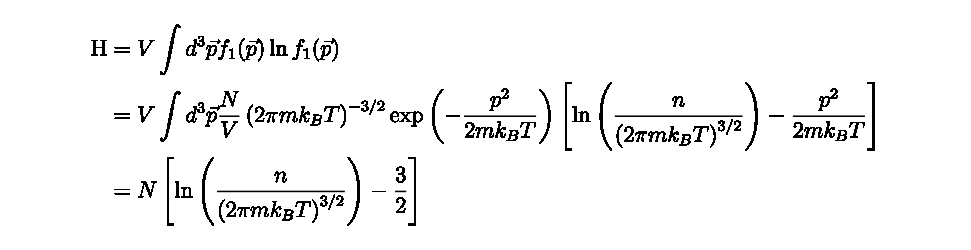

```mathematica
MaTeX["\\begin{aligned}\\mathrm{H} & =V \\int d^{3} \\vec{p} f_{1}(\\vec{p}) \\ln f_{1}(\\vec{p}) \\\\& =V \\int d^{3} \\vec{p} \\frac{N}{V}\\left(2 \\pi m k_{B} T\\right)^{-3 / 2} \\exp \\left(-\\frac{p^{2}}{2 m k_{B} T}\\right)\\left[\\ln \\left(\\frac{n}{\\left(2 \\pi m k_{B} T\\right)^{3 / 2}}\\right)-\\frac{p^{2}}{2 m k_{B} T}\\right] \\\\& =N\\left[\\ln \\left(\\frac{n}{\\left(2 \\pi m k_{B} T\\right)^{3 / 2}}\\right)-\\frac{3}{2}\\right]\\end{aligned}", Magnification -> 4]
```

```mathematica
(64) -- The entropy is now identified as
```

Statistical Mechanics
Ramirez (65)

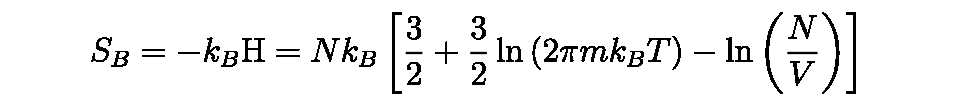

```mathematica
MaTeX["S_{B}=-k_{B} \\mathrm{H}=N k_{B}\\left[\\frac{3}{2}+\\frac{3}{2} \\ln \\left(2 \\pi m k_{B} T\\right)-\\ln \\left(\\frac{N}{V}\\right)\\right]", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["S_{B}=-k_{B} \\mathrm{H}=N k_{B}\\left[\\frac{3}{2}+\\frac{3}{2} \\ln \\left(2 \\pi m k_{B} T\\right)-\\ln \\left(\\frac{N}{V}\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S_B==-k_B H==N k_B[3/2+3/2 Log[2 π m k_B T]-Log[N/V]]

```mathematica
(66) -- In thermodynamics, we often encounter the equation T dS_B = dE + P dV. This simple yet powerful relation connects several important quantities in a system. Let's break it down:

T represents temperature, S_B is the Boltzmann entropy, E is the internal energy, P is pressure, and V is volume. The 'd' before each term indicates a small change in that quantity.

This equation tells us that when we add a small amount of heat to a system, it can cause two things to happen: the internal energy can increase (dE), and the system can expand against its surroundings (P dV). The left side of the equation (T dS_B) represents the heat added to the system.

Understanding this relationship helps us predict how systems behave when we change their temperature, volume, or energy, which is crucial in many real-world applications, from engines to refrigerators.
```

Statistical Mechanics
Ramirez (67)

```mathematica
MaTeX["\\begin{aligned}\\left.\\frac{\\partial E}{\\partial T}\\right|_{V} & =\\left.T \\frac{\\partial S_{B}}{\\partial T}\\right|_{V}=\\frac{3}{2} N k_{B} \\\\P+\\left.\\frac{\\partial E}{\\partial V}\\right|_{T} & =\\left.T \\frac{\\partial S_{B}}{\\partial V}\\right|_{T}=\\frac{N k_{B} T}{V}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(68) -- The behavior of a monatomic ideal gas. We can derive two important equations for this type of gas:

1. PV = NkT, which relates pressure (P), volume (V), number of particles (N), Boltzmann's constant (k), and temperature (T).

2. E = 3NkT/2, which gives us the total energy (E) of the gas.

These equations help us understand how the gas behaves under different conditions.

However, there's a catch when we look at very low temperatures. In classical physics, the entropy of this gas doesn't follow the third law of thermodynamics as we approach absolute zero. This means the entropy still depends on the gas density, which isn't what we'd expect based on quantum mechanics.
```

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

```mathematica
ThermoLecsDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"ThermoLecs24/"<>ThermoLecsDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear